# Infinite 3D medium, Isotropic Point Source, Lambert Sphere Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3DisopointLambertSpherescatter`"]
```

inf3DisopointLambertSpherescatter`

## Util

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

### Diffusion modes

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

## Analytical solutions

### Fluence: exact solution

[Grosjean 1963 - A New Approximate One-Velocity Theory for Treating both Isotropic and Anisotropic Multiple Scattering Problems, p. 37]

```mathematica
ϕexactTruncatedFourierOrder3[r_,Σt_,c_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((u^2 (135+60 c+256 u^2)+ArcTan[u] (15 (-2+c) (9+4 c) u+(-602+236 c) u^3+(-15 (-1+c) (9+4 c)+(346-c (281+20 c)) u^2+207 u^4) ArcTan[u]))/(u (-15 (-1+c) c (9+4 c) u+(301-256 c) c u^3+192 u^5+c (15 (-1+c) (9+4 c)+(-346+c (281+20 c)) u^2-207 u^4) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
ϕexactTruncatedFourierOrder5[r_,Σt_,c_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((u^2 (-700 c^2 (21+11 u^2)+35 c (5775+4753 u^2+16704 u^4)+48 (11025+11550 u^2+28945 u^4+49152 u^6))+u (-700 c^3 (21+11 u^2)+35 c^2 (6615+5333 u^2+16740 u^4)-288 (3675+5075 u^2+10605 u^4+19429 u^6)+2 c (62475+82670 u^2+94185 u^4+1084896 u^6)) ArcTan[u]+3 (140 c^3 (35+30 u^2+3 u^4)-7 c^2 (10325+11730 u^2+29685 u^4+9024 u^6)-c (109025+169365 u^2+304815 u^4+869739 u^6)+48 (3675+6300 u^2+11970 u^4+22684 u^6+13275 u^8)) ArcTan[u]^2)/(u (u (1769472 u^8+700 c^4 (21+11 u^2)-35 c^3 (6195+4973 u^2+16704 u^4)+144 c (3675+5075 u^2+10605 u^4+19429 u^6)-c^2 (327075+399070 u^2+810495 u^4+2359296 u^6))-3 c (140 c^3 (35+30 u^2+3 u^4)-7 c^2 (10325+11730 u^2+29685 u^4+9024 u^6)-c (109025+169365 u^2+304815 u^4+869739 u^6)+48 (3675+6300 u^2+11970 u^4+22684 u^6+13275 u^8)) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
ϕexactTruncatedFourierOrder7[r_,Σt_,c_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((u^2 (140140 c^3 (165+170 u^2+33 u^4)-77 c^2 (177101925+271313770 u^2+205154145 u^4+58729024 u^6)+112 c (1627701075+2990582595 u^2+2541654225 u^4+998391449 u^6+2162822400 u^8)+3072 (156080925+321621300 u^2+298676070 u^4+138244260 u^6+191491237 u^8+314572800 u^10))+u (140140 c^4 (165+170 u^2+33 u^4)-77 c^3 (177702525+272032670 u^2+205350705 u^4+58735524 u^6)+14 c^2 (14969729775+27232560355 u^2+22999478535 u^4+8921729839 u^6+17350020000 u^8)-92160 (10405395+24909885 u^2+26133954 u^4+14432110 u^6+14752395 u^8+24914165 u^10)+32 c (3589861275+8363415060 u^2+8389598910 u^4+4353077036 u^6+2659995975 u^8+27763977600 u^10)) ArcTan[u]-5 (20020 c^4 (231+315 u^2+105 u^4+5 u^6)-77 c^3 (35480445+66151449 u^2+55997235 u^4+22249895 u^6+1725120 u^8)+48 c (1238242005+3176672499 u^2+3513643210 u^4+2065779870 u^6+1757994945 u^8+4460927055 u^10)+c^2 (39187873725+84226438296 u^2+80326759590 u^4+38796268280 u^6+52992099405 u^8+15584071680 u^10)-46080 (2081079+5675670 u^2+6702465 u^4+4282740 u^6+3617145 u^8+5848054 u^10+3399375 u^12)) ArcTan[u]^2)/(u (u (724775731200 u^12-140140 c^5 (165+170 u^2+33 u^4)+77 c^4 (177402225+271623170 u^2+205214205 u^4+58729024 u^6)-7 c^3 (27991338375+50831295515 u^2+42920610645 u^4+16619786953 u^6+34605158400 u^8)+46080 c (10405395+24909885 u^2+26133954 u^4+14432110 u^6+14752395 u^8+24914165 u^10)-16 c^2 (18573630075+41458877460 u^2+40536011670 u^4+20295123772 u^6+21838535775 u^8+60397977600 u^10))+5 c (20020 c^4 (231+315 u^2+105 u^4+5 u^6)-77 c^3 (35480445+66151449 u^2+55997235 u^4+22249895 u^6+1725120 u^8)+48 c (1238242005+3176672499 u^2+3513643210 u^4+2065779870 u^6+1757994945 u^8+4460927055 u^10)+c^2 (39187873725+84226438296 u^2+80326759590 u^4+38796268280 u^6+52992099405 u^8+15584071680 u^10)-46080 (2081079+5675670 u^2+6702465 u^4+4282740 u^6+3617145 u^8+5848054 u^10+3399375 u^12)) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

### Rigorous asymptotic diffusion

```mathematica
Clear[c,b,g,x,v];
grosjeanΔ=buildΔ4[3]/.A[0]->1/.A[1]->-4/3/.A[2]->5/16;
dgrosjeanΔ=D[grosjeanΔ/.u->I v,c];
xpsolve=Solve[D[grosjeanΔ==0/.u->I x[c],c],x'[c]][[1,1,-1]];
grosjeang=buildg4[3]/.A[0]->1/.A[1]->-4/3/.A[2]->5/16/.u->I v;
```

```mathematica
(grosjeang(xpsolve x[c] 2/.x[c]->v))/dgrosjeanΔ/.Solve[grosjeanΔ==0/.u->I v,ArcTanh[v]]//FullSimplify
```

{-(18432 v^6 (-1+v^2))/(c (25 (-16+c) (-1+c)^2 (9+4 c)^2+2 (-1+c) (9+4 c) (-4568+c (3283+160 c)) v^2-9 (6640+c (-7417+1152 c)) v^4+9936 v^6))}

```mathematica
grosjeanΔ/.u->I V
```

1+(45 c)/(64 V^4)-(25 c^2)/(64 V^4)-(5 c^3)/(16 V^4)-(301 c)/(192 V^2)+(4 c^2)/(3 V^2)-(45 c ArcTanh[V])/(64 V^5)+(25 c^2 ArcTanh[V])/(64 V^5)+(5 c^3 ArcTanh[V])/(16 V^5)+(173 c ArcTanh[V])/(96 V^3)-(281 c^2 ArcTanh[V])/(192 V^3)-(5 c^3 ArcTanh[V])/(48 V^3)-(69 c ArcTanh[V])/(64 V)

```mathematica
LSv0inv[c_]:=ReplaceAll[Abs[V],FindRoot[1+(45 c)/(64 V^4)-(25 c^2)/(64 V^4)-(5 c^3)/(16 V^4)-(301 c)/(192 V^2)+(4 c^2)/(3 V^2)-(45 c ArcTanh[V])/(64 V^5)+(25 c^2 ArcTanh[V])/(64 V^5)+(5 c^3 ArcTanh[V])/(16 V^5)+(173 c ArcTanh[V])/(96 V^3)-(281 c^2 ArcTanh[V])/(192 V^3)-(5 c^3 ArcTanh[V])/(48 V^3)-(69 c ArcTanh[V])/(64 V),{V,0.8}]];
```

```mathematica
ϕrigourousDiffusion[r_,Σt_,c_]:=Σt/(4 Pi r)(-((18432 #1^6 (-1+#1^2))/(c (25 (-16+c) (-1+c)^2 (9+4 c)^2+2 (-1+c) (9+4 c) (-4568+c (3283+160 c)) #1^2-9 (6640+c (-7417+1152 c)) #1^4+9936 #1^6))))Exp[-# r Σt]&[LSv0inv[c]]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_LSscatter*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,13]];
α=data[[2,3]];
{α,Σt,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
numcollorders=simulations[[1]][[3]][[2,13]];
maxr=simulations[[1]][[3]][[2,5]];dr=simulations[[1]][[3]][[2,7]];
numr=Floor[maxr/dr];
```

## Compare MC and deterministic

### Fluence - Exact solution comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

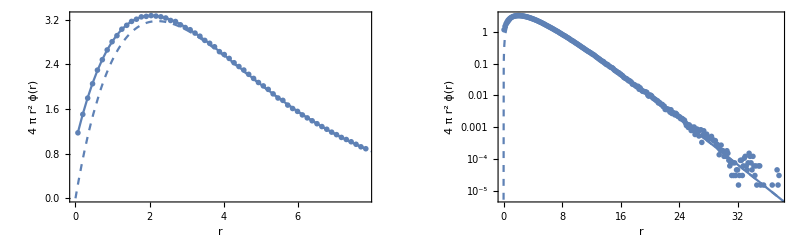

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[-1]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexactTruncatedFourierOrder3[#[[1]],1/mfp,c]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexactTruncatedFourierOrder3[#[[1]],1/mfp,c]}]& /@pointsFluence[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Plot[4 Pi r^2 ϕrigourousDiffusion[r,1/mfp,c],{r,0,maxr},PlotStyle->Dashed,PlotRange->All],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
LogPlot[4 Pi r^2 ϕrigourousDiffusion[r,1/mfp,c],{r,0,maxr},PlotStyle->Dashed,PlotRange->All],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (continuous) and Rigorous Asymptotic Diffusion (dashed)\nInfinite 3D, isotropic point source, Lambert-Sphere scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Compare moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

#### mfp 1

```mathematica
mfp=1;
sims1=Select[simulations,#[[2]]==mfp&];
```

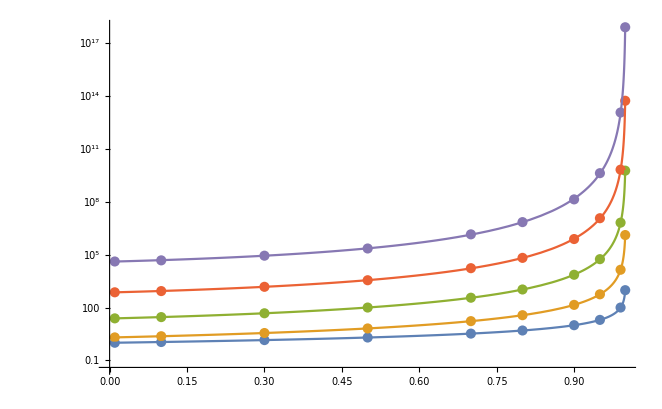

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),-3!mfp mfp^2/((-3-(4 c)/3) (-1+c)^2),5!mfp((9-(69 c)/16) mfp^4)/((-3-(4 c)/3)^2 (-5+(5 c)/16) (-1+c)^3),mfp 7!((-675+(5691 c)/8-(36399 c^2)/256-48 c^3) mfp^6)/(7 (-3-(4 c)/3)^3 (-5+(5 c)/16)^2 (-1+c)^4),mfp 9!((-496125+(52729425 c)/64-(367391171 c^2)/1024-(1099685881 c^3)/16384+(11363604819 c^4)/262144+(312487 c^5)/32-329 c^6) mfp^8)/(49 (-3-(4 c)/3)^4 (-9+c/64) (-5+(5 c)/16)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```

#### mfp 0.3

```mathematica
mfp=0.3;
sims1=Select[simulations,#[[2]]==mfp&];
```

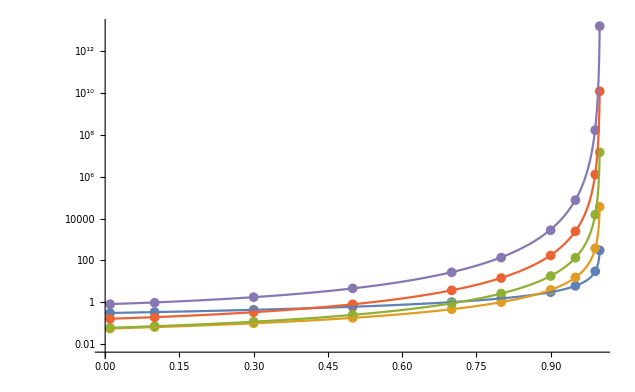

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),-3!mfp mfp^2/((-3-(4 c)/3) (-1+c)^2),5!mfp((9-(69 c)/16) mfp^4)/((-3-(4 c)/3)^2 (-5+(5 c)/16) (-1+c)^3),mfp 7!((-675+(5691 c)/8-(36399 c^2)/256-48 c^3) mfp^6)/(7 (-3-(4 c)/3)^3 (-5+(5 c)/16)^2 (-1+c)^4),mfp 9!((-496125+(52729425 c)/64-(367391171 c^2)/1024-(1099685881 c^3)/16384+(11363604819 c^4)/262144+(312487 c^5)/32-329 c^6) mfp^8)/(49 (-3-(4 c)/3)^4 (-9+c/64) (-5+(5 c)/16)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```

## Namespace

```mathematica
End[]
```